```mathematica
Cycloid
```

## We know the Cycloid equation is

x = R (θ - Sin[θ]); y = R (1 - Cos[θ]);

## and we can plot this trajectory.

```mathematica
R:=6;
Manipulate[Show[ParametricPlot[{α R+R Cos[-(π/2)-α],R+R Sin[-(π/2)-α]},{α,0,5 π},AspectRatio->Automatic]//Evaluate,Graphics[{Circle[{α R,R},R],Red,Thick,Line[{{α R+R Cos[-(π/2)-α],R+R Sin[-(π/2)-α]},{α R,R}}],PointSize[Large],Pink,Point[{α R+R Cos[-(π/2)-α],R+R Sin[-(π/2)-α]}]}]],{α,0,5 π}]
```

## and also we can change the parameter

```mathematica
R:=6;
a=Manipulate[Show[ParametricPlot[{α R+R Cos[-(π/2)-α]+α,R+R Sin[-(π/2)-α]+α},{α,0,5 π},AspectRatio->Automatic]//Evaluate,Graphics[{Circle[{α R+α,R+α},R],Red,Thick,Line[{{α R+R Cos[-(π/2)-α]+α,R+R Sin[-(π/2)-α]+α},{α R+α,R+α}}],PointSize[Large],Pink,Point[{α R+R Cos[-(π/2)-α]+α,R+R Sin[-(π/2)-α]+α}]}]],{α,0,5 π}]
```

## now we also can calculate the equation again via Ruler theory.

```mathematica
T1={{1,0,r*θ},{0,1,0},{0,0,1}};(*Linear motion---coordinate1*)
T2={{Cos[θ],Sin[θ],0},{-Sin[θ],Cos[θ],r},{0,0,1}};(*Rotation---coordinate2*)
P={{0},{-r},{1}};(*Initial position*)
T1.T2.P//MatrixForm
```

(6 θ-6 Sin[θ]
6-6 Cos[θ]
1)

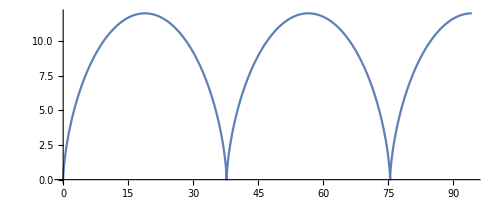

```mathematica
r=6;
ParametricPlot[{r θ-r Sin[θ],r-r Cos[θ]},{θ,0,5π},AspectRatio->Automatic]
```